# Notebook for: Numerical study of the gravitational shock wave inside a spherical charged black hole by Eilon & Ori

Geoff Cope
University of Utah
                                                                                                             𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
February 3, 2021

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Paper

```mathematica
Hyperlink["Numerical study of the gravitational shock wave inside a spherical charged black hole",
"https://arxiv.org/abs/1610.04355"]
```

[Numerical study of the gravitational shock wave inside a spherical charged black hole](https://arxiv.org/abs/1610.04355)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 6 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv ,
Dt[x]-> dx , 
Dt[y] -> dy , 
Dt[z]-> dz , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  , 
Dt[μ]-> dμ , 
Dt[η]-> dη , 
Dt[ν]-> dν , 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[ϱ]-> dϱ , 
Dt[φ] -> dφ ,
Dt[ξ]-> dξ ,  
Dt[Δ]-> dΔ , 
Dt[δ]-> dδ , 
Dt[ω]-> dω , 
 Dt[𝓉] -> d𝓉 , 
Dt[𝓋]-> d𝓋 , 
Dt[𝓊]-> d𝓊 ,
Dt[𝓍]-> d𝓍 ,
Dt[𝓎]-> d𝓎,   
Dt[𝓏] -> d𝓏,
Dt[T]-> dT,
Dt[X]-> dX, 
Dt[Y]-> dY,
Dt[Z]-> dZ,
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ
};
dtReplace // TableForm
```

Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[μ]→dμ
Dt[η]→dη
Dt[ν]→dν
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[ϱ]→dϱ
Dt[φ]→dφ
Dt[ξ]→dξ
Dt[Δ]→dΔ
Dt[δ]→dδ
Dt[ω]→dω
Dt[𝓉]→d𝓉
Dt[𝓋]→d𝓋
Dt[𝓊]→d𝓊
Dt[𝓍]→d𝓍
Dt[𝓎]→d𝓎
Dt[𝓏]→d𝓏
Dt[T]→dT
Dt[X]→dX
Dt[Y]→dY
Dt[Z]→dZ
Dt[U]→dU
Dt[V]→dV
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ

```mathematica
a/:Dt[a]=0  ;  
b /: Dt[b] = 0 ;  
M /: Dt[M] = 0 ;  (* For Schwarzschild Mass *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 1: Double Null Coordinates

```mathematica
Clear[eq1]
eq1 = 
-  Exp[σ[u,v]] du dv + r[u,v]^2 ( dθ^2+ Sin[θ]^2 dϕ^2)
```

-du dv ⅇ^σ[u,v]+r[u,v]^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric1]
metric1 = 
lineToMetric[ eq1 , {du,dv,dθ,dϕ}] ;
metric1 // MatrixForm
```

(0 | -1/2 ⅇ^σ[u,v] | 0 | 0
-1/2 ⅇ^σ[u,v] | 0 | 0 | 0
0 | 0 | r[u,v]^2 | 0
0 | 0 | 0 | r[u,v]^2 Sin[θ]^2)

```mathematica
Clear[inverse1]
inverse1 = 
Inverse[ metric1 ] // Expand // Simplify ;
inverse1 // MatrixForm // pdConv
```

(0 | -2 ⅇ^(-σ(u,v)) | 0 | 0
-2 ⅇ^(-σ(u,v)) | 0 | 0 | 0
0 | 0 | 1/(r(u,v))^2 | 0
0 | 0 | 0 | (csc^2(θ))/(r(u,v))^2)

```mathematica
metric1 . inverse1 // Expand // Simplify // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
inverse1 . metric1 // Expand // Simplify // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## Calculation of Tensors For Metric 1: Double Null Coordinates

```mathematica
Clear[input] 
input[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList];
tensorList = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList[[2]]  = 
ChristoffelSymbol[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[3]] = 
RiemannTensor[ tensorList[[1]] , ActWithNested-> Simplify ];
tensorList[[4]] = 
RicciTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[5]] = 
RicciScalar[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[6]] = 
KretschmannScalar[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[7]] = 
EinsteinTensor[ tensorList[[1]] , ActWith-> Simplify] ; 
tensorList[[8]] = 
WeylTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
 tensorList[[9]] = 
CottonTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
];
```

```mathematica
(* Last timing took 4.88 for all tensors *)
input[ "metric1", metric1, "DoubleNull","g^dn",{u,v,θ,ϕ}, "Greek"] // Timing
```

{5.19462,Null}

```mathematica
tensorList[[1]]
TensorName[tensorList[[1]]]
TensorValues[tensorList[[1]]] // MatrixForm // pdConv
```

(g^dn)_αβ^

DoubleNull

(0 | -1/2 ⅇ^(σ(u,v)) | 0 | 0
-1/2 ⅇ^(σ(u,v)) | 0 | 0 | 0
0 | 0 | (r(u,v))^2 | 0
0 | 0 | 0 | sin^2(θ) (r(u,v))^2)

```mathematica
tensorList[[2]]
TensorName[tensorList[[2]]]
TensorValues[tensorList[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolDoubleNull

(((∂σ(u,v))/(∂u)
0
0
0) | (0
0
0
0) | (0
0
2 r(u,v) ⅇ^(-σ(u,v)) (∂r(u,v))/(∂v)
0) | (0
0
0
2 sin^2(θ) r(u,v) ⅇ^(-σ(u,v)) (∂r(u,v))/(∂v))
(0
0
0
0) | (0
(∂σ(u,v))/(∂v)
0
0) | (0
0
2 r(u,v) ⅇ^(-σ(u,v)) (∂r(u,v))/(∂u)
0) | (0
0
0
2 sin^2(θ) r(u,v) ⅇ^(-σ(u,v)) (∂r(u,v))/(∂u))
(0
0
((∂r(u,v))/(∂u))/(r(u,v))
0) | (0
0
((∂r(u,v))/(∂v))/(r(u,v))
0) | (((∂r(u,v))/(∂u))/(r(u,v))
((∂r(u,v))/(∂v))/(r(u,v))
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
((∂r(u,v))/(∂u))/(r(u,v))) | (0
0
0
((∂r(u,v))/(∂v))/(r(u,v))) | (0
0
0
cot(θ)) | (((∂r(u,v))/(∂u))/(r(u,v))
((∂r(u,v))/(∂v))/(r(u,v))
cot(θ)
0))

```mathematica
tensorList[[3]]
TensorName[tensorList[[3]]]
TensorValues[tensorList[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorDoubleNull

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -1/2 ⅇ^(σ(u,v)) (∂^2 σ(u,v))/(∂u ∂v) | 0 | 0
1/2 ⅇ^(σ(u,v)) (∂^2 σ(u,v))/(∂u ∂v) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | r(u,v) ((∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)-(∂^2 r(u,v))/(∂u^2)) | 0
0 | 0 | r(u,v) (-(∂^2 r(u,v))/(∂u ∂v)) | 0
-(r(u,v) ((∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)-(∂^2 r(u,v))/(∂u^2))) | r(u,v) (∂^2 r(u,v))/(∂u ∂v) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | sin^2(θ) r(u,v) ((∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)-(∂^2 r(u,v))/(∂u^2))
0 | 0 | 0 | sin^2(θ) r(u,v) (-(∂^2 r(u,v))/(∂u ∂v))
0 | 0 | 0 | 0
-(sin^2(θ) r(u,v) ((∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)-(∂^2 r(u,v))/(∂u^2))) | sin^2(θ) r(u,v) (∂^2 r(u,v))/(∂u ∂v) | 0 | 0)
(0 | 1/2 ⅇ^(σ(u,v)) (∂^2 σ(u,v))/(∂u ∂v) | 0 | 0
-1/2 ⅇ^(σ(u,v)) (∂^2 σ(u,v))/(∂u ∂v) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | r(u,v) (-(∂^2 r(u,v))/(∂u ∂v)) | 0
0 | 0 | r(u,v) ((∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)-(∂^2 r(u,v))/(∂v^2)) | 0
r(u,v) (∂^2 r(u,v))/(∂u ∂v) | -(r(u,v) ((∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)-(∂^2 r(u,v))/(∂v^2))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | sin^2(θ) r(u,v) (-(∂^2 r(u,v))/(∂u ∂v))
0 | 0 | 0 | sin^2(θ) r(u,v) ((∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)-(∂^2 r(u,v))/(∂v^2))
0 | 0 | 0 | 0
sin^2(θ) r(u,v) (∂^2 r(u,v))/(∂u ∂v) | -(sin^2(θ) r(u,v) ((∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)-(∂^2 r(u,v))/(∂v^2))) | 0 | 0)
(0 | 0 | -(r(u,v) ((∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)-(∂^2 r(u,v))/(∂u^2))) | 0
0 | 0 | r(u,v) (∂^2 r(u,v))/(∂u ∂v) | 0
r(u,v) ((∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)-(∂^2 r(u,v))/(∂u^2)) | r(u,v) (-(∂^2 r(u,v))/(∂u ∂v)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | r(u,v) (∂^2 r(u,v))/(∂u ∂v) | 0
0 | 0 | -(r(u,v) ((∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)-(∂^2 r(u,v))/(∂v^2))) | 0
r(u,v) (-(∂^2 r(u,v))/(∂u ∂v)) | r(u,v) ((∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)-(∂^2 r(u,v))/(∂v^2)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | sin^2(θ) (r(u,v))^2 ⅇ^(-σ(u,v)) (4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v)))
0 | 0 | sin^2(θ) (r(u,v))^2 (-ⅇ^(-σ(u,v))) (4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))) | 0)
(0 | 0 | 0 | -(sin^2(θ) r(u,v) ((∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)-(∂^2 r(u,v))/(∂u^2)))
0 | 0 | 0 | sin^2(θ) r(u,v) (∂^2 r(u,v))/(∂u ∂v)
0 | 0 | 0 | 0
sin^2(θ) r(u,v) ((∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)-(∂^2 r(u,v))/(∂u^2)) | sin^2(θ) r(u,v) (-(∂^2 r(u,v))/(∂u ∂v)) | 0 | 0) | (0 | 0 | 0 | sin^2(θ) r(u,v) (∂^2 r(u,v))/(∂u ∂v)
0 | 0 | 0 | -(sin^2(θ) r(u,v) ((∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)-(∂^2 r(u,v))/(∂v^2)))
0 | 0 | 0 | 0
sin^2(θ) r(u,v) (-(∂^2 r(u,v))/(∂u ∂v)) | sin^2(θ) r(u,v) ((∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)-(∂^2 r(u,v))/(∂v^2)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | sin^2(θ) (r(u,v))^2 (-ⅇ^(-σ(u,v))) (4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v)))
0 | 0 | sin^2(θ) (r(u,v))^2 ⅇ^(-σ(u,v)) (4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[4]]
TensorName[tensorList[[4]]]
TensorValues[tensorList[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorDoubleNull

((2 (∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)-2 (∂^2 r(u,v))/(∂u^2))/(r(u,v)) | -(2 (∂^2 r(u,v))/(∂u ∂v))/(r(u,v))-(∂^2 σ(u,v))/(∂u ∂v) | 0 | 0
-(2 (∂^2 r(u,v))/(∂u ∂v))/(r(u,v))-(∂^2 σ(u,v))/(∂u ∂v) | (2 (∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)-2 (∂^2 r(u,v))/(∂v^2))/(r(u,v)) | 0 | 0
0 | 0 | ⅇ^(-σ(u,v)) (4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))) | 0
0 | 0 | 0 | sin^2(θ) ⅇ^(-σ(u,v)) (4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))))

```mathematica
tensorList[[5]]
TensorName[tensorList[[5]]]
TensorValues[tensorList[[5]]] // MatrixForm // pdConv
```

R

RicciScalarDoubleNull

(2 ⅇ^(-σ(u,v)) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)+8 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))))/(r(u,v))^2

```mathematica
tensorList[[6]]
TensorName[tensorList[[6]]]
TensorValues[tensorList[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarDoubleNull

(4 ⅇ^(-2 σ(u,v)) (16 (r(u,v))^2 (((∂^2 r(u,v))/(∂u ∂v))^2+(∂^2 r(u,v))/(∂v^2) ((∂^2 r(u,v))/(∂u^2)-(∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)))+4 (r(u,v))^4 ((∂^2 σ(u,v))/(∂u ∂v))^2+8 (∂r(u,v))/(∂v) ((∂r(u,v))/(∂u) (2 (r(u,v))^2 (∂σ(u,v))/(∂u) (∂σ(u,v))/(∂v)+ⅇ^(σ(u,v)))-2 (r(u,v))^2 (∂^2 r(u,v))/(∂u^2) (∂σ(u,v))/(∂v))+16 ((∂r(u,v))/(∂u))^2 ((∂r(u,v))/(∂v))^2+ⅇ^(2 σ(u,v))))/(r(u,v))^4

```mathematica
tensorList[[7]]
TensorName[tensorList[[7]]]
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorDoubleNull

((2 (∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)-2 (∂^2 r(u,v))/(∂u^2))/(r(u,v)) | (4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v)))/(2 (r(u,v))^2) | 0 | 0
(4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v)))/(2 (r(u,v))^2) | (2 (∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)-2 (∂^2 r(u,v))/(∂v^2))/(r(u,v)) | 0 | 0
0 | 0 | -2 r(u,v) ⅇ^(-σ(u,v)) (r(u,v) (∂^2 σ(u,v))/(∂u ∂v)+2 (∂^2 r(u,v))/(∂u ∂v)) | 0
0 | 0 | 0 | -2 sin^2(θ) r(u,v) ⅇ^(-σ(u,v)) (r(u,v) (∂^2 σ(u,v))/(∂u ∂v)+2 (∂^2 r(u,v))/(∂u ∂v)))

```mathematica
tensorList[[8]]
TensorName[tensorList[[8]]]
TensorValues[tensorList[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorDoubleNull

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -(ⅇ^(σ(u,v)) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))))/(12 (r(u,v))^2) | 0 | 0
(ⅇ^(σ(u,v)) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))))/(12 (r(u,v))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1/12 (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))) | 0
0 | 1/12 (-2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)+4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)-4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)-ⅇ^(σ(u,v))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 1/12 sin^2(θ) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v)))
0 | 0 | 0 | 0
0 | -1/12 sin^2(θ) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))) | 0 | 0)
(0 | (ⅇ^(σ(u,v)) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))))/(12 (r(u,v))^2) | 0 | 0
-(ⅇ^(σ(u,v)) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))))/(12 (r(u,v))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/12 (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))) | 0
0 | 0 | 0 | 0
1/12 (-2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)+4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)-4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)-ⅇ^(σ(u,v))) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 1/12 sin^2(θ) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v)))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/12 sin^2(θ) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))) | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 1/12 (-2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)+4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)-4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)-ⅇ^(σ(u,v))) | 0
0 | 1/12 (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/12 (-2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)+4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)-4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)-ⅇ^(σ(u,v))) | 0
0 | 0 | 0 | 0
1/12 (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/3 sin^2(θ) (r(u,v))^2 ⅇ^(-σ(u,v)) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v)))
0 | 0 | -1/3 sin^2(θ) (r(u,v))^2 ⅇ^(-σ(u,v)) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))) | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | -1/12 sin^2(θ) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v)))
0 | 0 | 0 | 0
0 | 1/12 sin^2(θ) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))) | 0 | 0) | (0 | 0 | 0 | -1/12 sin^2(θ) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v)))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/12 sin^2(θ) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1/3 sin^2(θ) (r(u,v))^2 ⅇ^(-σ(u,v)) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v)))
0 | 0 | 1/3 sin^2(θ) (r(u,v))^2 ⅇ^(-σ(u,v)) (2 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v))) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[9]]
TensorName[tensorList[[9]]]
TensorValues[tensorList[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorDoubleNull

((0
(2 r(u,v) ((r(u,v))^2 ((∂^3 σ(u,v))/(∂u^2 ∂v)-(∂σ(u,v))/(∂u) (∂^2 σ(u,v))/(∂u ∂v))+2 r(u,v) ((∂σ(u,v))/(∂u) (∂^2 r(u,v))/(∂u ∂v)-(∂^3 r(u,v))/(∂u^2 ∂v))+2 (∂r(u,v))/(∂v) (∂^2 r(u,v))/(∂u^2))+(∂r(u,v))/(∂u) (6 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) ((∂^2 r(u,v))/(∂u ∂v)+(∂r(u,v))/(∂v) (∂σ(u,v))/(∂u))+ⅇ^(σ(u,v)))+4 (∂r(u,v))/(∂v) ((∂r(u,v))/(∂u))^2)/(3 (r(u,v))^3)
0
0) | (-(2 r(u,v) ((r(u,v))^2 ((∂^3 σ(u,v))/(∂u^2 ∂v)-(∂σ(u,v))/(∂u) (∂^2 σ(u,v))/(∂u ∂v))+2 r(u,v) ((∂σ(u,v))/(∂u) (∂^2 r(u,v))/(∂u ∂v)-(∂^3 r(u,v))/(∂u^2 ∂v))+2 (∂r(u,v))/(∂v) (∂^2 r(u,v))/(∂u^2))+(∂r(u,v))/(∂u) (6 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) ((∂^2 r(u,v))/(∂u ∂v)+(∂r(u,v))/(∂v) (∂σ(u,v))/(∂u))+ⅇ^(σ(u,v)))+4 (∂r(u,v))/(∂v) ((∂r(u,v))/(∂u))^2)/(3 (r(u,v))^3)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
-(2 r(u,v) (r(u,v) (r(u,v) (∂^3 σ(u,v))/(∂u ∂v^2)-2 (∂^3 r(u,v))/(∂u ∂v^2)+(∂σ(u,v))/(∂v) (2 (∂^2 r(u,v))/(∂u ∂v)-r(u,v) (∂^2 σ(u,v))/(∂u ∂v)))+2 (∂r(u,v))/(∂u) (∂^2 r(u,v))/(∂v^2))+(∂r(u,v))/(∂v) (6 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) ((∂^2 r(u,v))/(∂u ∂v)+(∂r(u,v))/(∂u) (∂σ(u,v))/(∂v))+ⅇ^(σ(u,v)))+4 (∂r(u,v))/(∂u) ((∂r(u,v))/(∂v))^2)/(3 (r(u,v))^3)
0
0) | ((2 r(u,v) (r(u,v) (r(u,v) (∂^3 σ(u,v))/(∂u ∂v^2)-2 (∂^3 r(u,v))/(∂u ∂v^2)+(∂σ(u,v))/(∂v) (2 (∂^2 r(u,v))/(∂u ∂v)-r(u,v) (∂^2 σ(u,v))/(∂u ∂v)))+2 (∂r(u,v))/(∂u) (∂^2 r(u,v))/(∂v^2))+(∂r(u,v))/(∂v) (6 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) ((∂^2 r(u,v))/(∂u ∂v)+(∂r(u,v))/(∂u) (∂σ(u,v))/(∂v))+ⅇ^(σ(u,v)))+4 (∂r(u,v))/(∂u) ((∂r(u,v))/(∂v))^2)/(3 (r(u,v))^3)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
(ⅇ^(-σ(u,v)) (2 r(u,v) ((r(u,v))^2 ((∂^3 σ(u,v))/(∂u^2 ∂v)-(∂σ(u,v))/(∂u) (∂^2 σ(u,v))/(∂u ∂v))+2 r(u,v) ((∂σ(u,v))/(∂u) (∂^2 r(u,v))/(∂u ∂v)-(∂^3 r(u,v))/(∂u^2 ∂v))+2 (∂r(u,v))/(∂v) (∂^2 r(u,v))/(∂u^2))+(∂r(u,v))/(∂u) (6 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) ((∂^2 r(u,v))/(∂u ∂v)+(∂r(u,v))/(∂v) (∂σ(u,v))/(∂u))+ⅇ^(σ(u,v)))+4 (∂r(u,v))/(∂v) ((∂r(u,v))/(∂u))^2))/(3 r(u,v))
0) | (0
0
(ⅇ^(-σ(u,v)) (2 r(u,v) (r(u,v) (r(u,v) (∂^3 σ(u,v))/(∂u ∂v^2)-2 (∂^3 r(u,v))/(∂u ∂v^2)+(∂σ(u,v))/(∂v) (2 (∂^2 r(u,v))/(∂u ∂v)-r(u,v) (∂^2 σ(u,v))/(∂u ∂v)))+2 (∂r(u,v))/(∂u) (∂^2 r(u,v))/(∂v^2))+(∂r(u,v))/(∂v) (6 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) ((∂^2 r(u,v))/(∂u ∂v)+(∂r(u,v))/(∂u) (∂σ(u,v))/(∂v))+ⅇ^(σ(u,v)))+4 (∂r(u,v))/(∂u) ((∂r(u,v))/(∂v))^2))/(3 r(u,v))
0) | ((ⅇ^(-σ(u,v)) (2 r(u,v) ((r(u,v))^2 ((∂σ(u,v))/(∂u) (∂^2 σ(u,v))/(∂u ∂v)-(∂^3 σ(u,v))/(∂u^2 ∂v))+r(u,v) (2 (∂^3 r(u,v))/(∂u^2 ∂v)-2 (∂σ(u,v))/(∂u) (∂^2 r(u,v))/(∂u ∂v))-2 (∂r(u,v))/(∂v) (∂^2 r(u,v))/(∂u^2))-(∂r(u,v))/(∂u) (6 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) ((∂^2 r(u,v))/(∂u ∂v)+(∂r(u,v))/(∂v) (∂σ(u,v))/(∂u))+ⅇ^(σ(u,v)))-4 (∂r(u,v))/(∂v) ((∂r(u,v))/(∂u))^2))/(3 r(u,v))
(ⅇ^(-σ(u,v)) (2 r(u,v) (r(u,v) (-r(u,v) (∂^3 σ(u,v))/(∂u ∂v^2)+2 (∂^3 r(u,v))/(∂u ∂v^2)+(∂σ(u,v))/(∂v) (r(u,v) (∂^2 σ(u,v))/(∂u ∂v)-2 (∂^2 r(u,v))/(∂u ∂v)))-2 (∂r(u,v))/(∂u) (∂^2 r(u,v))/(∂v^2))-(∂r(u,v))/(∂v) (6 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) ((∂^2 r(u,v))/(∂u ∂v)+(∂r(u,v))/(∂u) (∂σ(u,v))/(∂v))+ⅇ^(σ(u,v)))-4 (∂r(u,v))/(∂u) ((∂r(u,v))/(∂v))^2))/(3 r(u,v))
0
0) | (0
0
0
0)
(0
0
0
(sin^2(θ) ⅇ^(-σ(u,v)) (2 r(u,v) ((r(u,v))^2 ((∂^3 σ(u,v))/(∂u^2 ∂v)-(∂σ(u,v))/(∂u) (∂^2 σ(u,v))/(∂u ∂v))+2 r(u,v) ((∂σ(u,v))/(∂u) (∂^2 r(u,v))/(∂u ∂v)-(∂^3 r(u,v))/(∂u^2 ∂v))+2 (∂r(u,v))/(∂v) (∂^2 r(u,v))/(∂u^2))+(∂r(u,v))/(∂u) (6 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) ((∂^2 r(u,v))/(∂u ∂v)+(∂r(u,v))/(∂v) (∂σ(u,v))/(∂u))+ⅇ^(σ(u,v)))+4 (∂r(u,v))/(∂v) ((∂r(u,v))/(∂u))^2))/(3 r(u,v))) | (0
0
0
(sin^2(θ) ⅇ^(-σ(u,v)) (2 r(u,v) (r(u,v) (r(u,v) (∂^3 σ(u,v))/(∂u ∂v^2)-2 (∂^3 r(u,v))/(∂u ∂v^2)+(∂σ(u,v))/(∂v) (2 (∂^2 r(u,v))/(∂u ∂v)-r(u,v) (∂^2 σ(u,v))/(∂u ∂v)))+2 (∂r(u,v))/(∂u) (∂^2 r(u,v))/(∂v^2))+(∂r(u,v))/(∂v) (6 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) ((∂^2 r(u,v))/(∂u ∂v)+(∂r(u,v))/(∂u) (∂σ(u,v))/(∂v))+ⅇ^(σ(u,v)))+4 (∂r(u,v))/(∂u) ((∂r(u,v))/(∂v))^2))/(3 r(u,v))) | (0
0
0
0) | (-(sin^2(θ) ⅇ^(-σ(u,v)) (2 r(u,v) ((r(u,v))^2 ((∂^3 σ(u,v))/(∂u^2 ∂v)-(∂σ(u,v))/(∂u) (∂^2 σ(u,v))/(∂u ∂v))+2 r(u,v) ((∂σ(u,v))/(∂u) (∂^2 r(u,v))/(∂u ∂v)-(∂^3 r(u,v))/(∂u^2 ∂v))+2 (∂r(u,v))/(∂v) (∂^2 r(u,v))/(∂u^2))+(∂r(u,v))/(∂u) (6 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) ((∂^2 r(u,v))/(∂u ∂v)+(∂r(u,v))/(∂v) (∂σ(u,v))/(∂u))+ⅇ^(σ(u,v)))+4 (∂r(u,v))/(∂v) ((∂r(u,v))/(∂u))^2))/(3 r(u,v))
-(sin^2(θ) ⅇ^(-σ(u,v)) (2 r(u,v) (r(u,v) (r(u,v) (∂^3 σ(u,v))/(∂u ∂v^2)-2 (∂^3 r(u,v))/(∂u ∂v^2)+(∂σ(u,v))/(∂v) (2 (∂^2 r(u,v))/(∂u ∂v)-r(u,v) (∂^2 σ(u,v))/(∂u ∂v)))+2 (∂r(u,v))/(∂u) (∂^2 r(u,v))/(∂v^2))+(∂r(u,v))/(∂v) (6 (r(u,v))^2 (∂^2 σ(u,v))/(∂u ∂v)-4 r(u,v) ((∂^2 r(u,v))/(∂u ∂v)+(∂r(u,v))/(∂u) (∂σ(u,v))/(∂v))+ⅇ^(σ(u,v)))+4 (∂r(u,v))/(∂u) ((∂r(u,v))/(∂v))^2))/(3 r(u,v))
0
0))

## Derivation of Vacuum Field Equations For Metric 1: Double Null Coordinates

```mathematica
Clear[nonzeroRicci] 
nonzeroRicci = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList[[4]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroRicci // TableForm // pdConv
```

(2 (∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)-2 (∂^2 r(u,v))/(∂u^2))/(r(u,v))
-(2 (∂^2 r(u,v))/(∂u ∂v))/(r(u,v))-(∂^2 σ(u,v))/(∂u ∂v)
(2 (∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)-2 (∂^2 r(u,v))/(∂v^2))/(r(u,v))
ⅇ^(-σ(u,v)) (4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v)))
sin^2(θ) ⅇ^(-σ(u,v)) (4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v)))

```mathematica
Clear[nonzeroEinstein] 
nonzeroEinstein = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList[[7]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroEinstein // TableForm // pdConv
```

(2 (∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)-2 (∂^2 r(u,v))/(∂u^2))/(r(u,v))
(4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v)))/(2 (r(u,v))^2)
(2 (∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)-2 (∂^2 r(u,v))/(∂v^2))/(r(u,v))
-2 r(u,v) ⅇ^(-σ(u,v)) (r(u,v) (∂^2 σ(u,v))/(∂u ∂v)+2 (∂^2 r(u,v))/(∂u ∂v))
-2 sin^2(θ) r(u,v) ⅇ^(-σ(u,v)) (r(u,v) (∂^2 σ(u,v))/(∂u ∂v)+2 (∂^2 r(u,v))/(∂u ∂v))

```mathematica
Clear[phi]
phi = 
ToTensor[{"PhiScalar","Φ"} , tensorList[[1]] , Φ[u,v] ]
```

Φ

```mathematica
Timing[waveScalar1=CovariantD[phi,-α,α]]
```

{0.021613,(g^dn)_^αβ (-Γ_αβ^γ (∂Φ)_γ^+(∂(∂Φ))_βα^)}

```mathematica
(* Klein Gordon Equation *) 

Clear[eq2a]
eq2a = 
( Flatten[Solve[ TensorValues[MergeTensors[waveScalar1] ] ==0 ,  Derivative[1,1][Φ][u,v]]][[1]] /. Rule-> Equal ) // Expand // Apart // Expand  ;
eq2a // pdConv
```

(∂^2 Φ(u,v))/(∂u ∂v)==-((∂r(u,v))/(∂v) (∂Φ(u,v))/(∂u))/(r(u,v))-((∂r(u,v))/(∂u) (∂Φ(u,v))/(∂v))/(r(u,v))

```mathematica
Clear[eq3a]
eq3a =
Flatten[Solve[ nonzeroEinstein[[2]] == 0 , Derivative[1,1][r][u,v] ]][[1]]/. Rule-> Equal // Expand  ;
eq3a// pdConv
```

(∂^2 r(u,v))/(∂u ∂v)==-ⅇ^(σ(u,v))/(4 r(u,v))-((∂r(u,v))/(∂u) (∂r(u,v))/(∂v))/(r(u,v))

```mathematica
Clear[eq4a]
eq4a =
Flatten[Solve[nonzeroEinstein[[4]]==0,Derivative[1,1][σ][u,v]]][[1]] /. Rule-> Equal ;
eq4a   // pdConv
```

(∂^2 σ(u,v))/(∂u ∂v)==-(2 (∂^2 r(u,v))/(∂u ∂v))/(r(u,v))

```mathematica
Clear[eq5a]
eq5a =
Flatten[Solve[nonzeroRicci[[1]] == 0 , Derivative[2,0][r][u,v ] ]][[1]] /. Rule-> Equal ;
eq5a  // pdConv
```

(∂^2 r(u,v))/(∂u^2)==(∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)

```mathematica
Clear[eq6a]
eq6a =
Flatten[Solve[nonzeroRicci[[3]] == 0 , Derivative[0,2][r][u,v ] ]][[1]] /. Rule-> Equal ;
eq6a  // pdConv
```

(∂^2 r(u,v))/(∂v^2)==(∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)

## Scalar Stress Energy Tensor

```mathematica
CovariantD[phi,-μ]CovariantD[phi,-ν]
MergeTensors[CovariantD[phi,-μ]CovariantD[phi,-ν]]

Clear[scalarSETtermOne]
scalarSETtermOne = 
TensorValues[MergeTensors[CovariantD[phi,-μ]CovariantD[phi,-ν]]] ;
scalarSETtermOne // MatrixForm // pdConv
```

(∂Φ)_μ^ (∂Φ)_ν^

((∂Φ)·(∂Φ))_μν^

(((∂Φ(u,v))/(∂u))^2 | (∂Φ(u,v))/(∂u) (∂Φ(u,v))/(∂v) | 0 | 0
(∂Φ(u,v))/(∂u) (∂Φ(u,v))/(∂v) | ((∂Φ(u,v))/(∂v))^2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList[[1]][-μ,-ν]tensorList[[1]][α,β]CovariantD[phi,-α]CovariantD[phi,-β]
MergeTensors[tensorList[[1]][-μ,-ν]tensorList[[1]][α,β]CovariantD[phi,-α]CovariantD[phi,-β]]

Clear[scalarSETtermTwo]
scalarSETtermTwo = 
TensorValues[MergeTensors[tensorList[[1]][-μ,-ν]tensorList[[1]][α,β]CovariantD[phi,-α]CovariantD[phi,-β]]] ;
scalarSETtermTwo // MatrixForm // pdConv
```

(g^dn)_^αβ (g^dn)_μν^ (∂Φ)_α^ (∂Φ)_β^

(((g^dn·g^dn)·(∂Φ))·(∂Φ))_μν^

(0 | 2 (∂Φ(u,v))/(∂u) (∂Φ(u,v))/(∂v) | 0 | 0
2 (∂Φ(u,v))/(∂u) (∂Φ(u,v))/(∂v) | 0 | 0 | 0
0 | 0 | -4 (r(u,v))^2 ⅇ^(-σ(u,v)) (∂Φ(u,v))/(∂u) (∂Φ(u,v))/(∂v) | 0
0 | 0 | 0 | -4 sin^2(θ) (r(u,v))^2 ⅇ^(-σ(u,v)) (∂Φ(u,v))/(∂u) (∂Φ(u,v))/(∂v))

```mathematica
Clear[scalarSETcomponents]
scalarSETcomponents = 
(1/(4π))( scalarSETtermOne-1/2 scalarSETtermTwo )    ;
scalarSETcomponents // MatrixForm // pdConv
```

(((∂Φ(u,v))/(∂u))^2/(4 π) | 0 | 0 | 0
0 | ((∂Φ(u,v))/(∂v))^2/(4 π) | 0 | 0
0 | 0 | ((r(u,v))^2 ⅇ^(-σ(u,v)) (∂Φ(u,v))/(∂u) (∂Φ(u,v))/(∂v))/(2 π) | 0
0 | 0 | 0 | (sin^2(θ) (r(u,v))^2 ⅇ^(-σ(u,v)) (∂Φ(u,v))/(∂u) (∂Φ(u,v))/(∂v))/(2 π))

```mathematica
Clear[Ts]
Ts = ToTensor["Ts" , tensorList[[1]] ,scalarSETcomponents , {-μ,-ν}]
```

Ts_μν^

## Maxwell Stress Energy Tensor

```mathematica
Clear[F]
F = 
Q({{0, (-Exp[σ[u,v]])/(2 r[u,v]^2), 0, 0}, {Exp[σ[u,v]]/(2 r[u,v]^2), 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})  ;
F // MatrixForm // pdConv
```

(0 | -(Q ⅇ^(σ(u,v)))/(2 (r(u,v))^2) | 0 | 0
(Q ⅇ^(σ(u,v)))/(2 (r(u,v))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Clear[ℱ]
ℱ = ToTensor["ℱ" , tensorList[[1]] ,F , {-μ,-ν}]
```

ℱ_μν^

```mathematica
tensorList[[1]][α,β]ℱ[-μ,-α] ℱ[-ν,-β]
MergeTensors[tensorList[[1]][α,β]ℱ[-μ,-α] ℱ[-ν,-β]]

Clear[setMaxwellTermOne]
setMaxwellTermOne = 
TensorValues[MergeTensors[tensorList[[1]][α,β]ℱ[-μ,-α] ℱ[-ν,-β]]] ;
setMaxwellTermOne // MatrixForm // pdConv
```

(g^dn)_^αβ ℱ_μα^ ℱ_νβ^

((g^dn·ℱ)·ℱ)_μν^

(0 | (Q^2 ⅇ^(σ(u,v)))/(2 (r(u,v))^4) | 0 | 0
(Q^2 ⅇ^(σ(u,v)))/(2 (r(u,v))^4) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList[[1]][-μ,-ν] ℱ[-α,-β]  ℱ[α,β] 
MergeTensors[tensorList[[1]][-μ,-ν] ℱ[-α,-β]  ℱ[α,β] ]

Clear[setMaxwellTermTwo]
setMaxwellTermTwo =
TensorValues[MergeTensors[tensorList[[1]][-μ,-ν] ℱ[-α,-β]  ℱ[α,β] ]]  ;
setMaxwellTermTwo // MatrixForm // pdConv
```

(g^dn)_μν^ ℱ_αβ^ ℱ_^αβ

((g^dn·ℱ)·ℱ)_μν^

(0 | (Q^2 ⅇ^(σ(u,v)))/(r(u,v))^4 | 0 | 0
(Q^2 ⅇ^(σ(u,v)))/(r(u,v))^4 | 0 | 0 | 0
0 | 0 | -(2 Q^2)/(r(u,v))^2 | 0
0 | 0 | 0 | -(2 Q^2 sin^2(θ))/(r(u,v))^2)

```mathematica
Clear[maxwellSETcomponents]
maxwellSETcomponents = 
(1/(4π))( setMaxwellTermOne  - (1/4)*setMaxwellTermTwo )  ;
maxwellSETcomponents  // MatrixForm // pdConv
```

(0 | (Q^2 ⅇ^(σ(u,v)))/(16 π (r(u,v))^4) | 0 | 0
(Q^2 ⅇ^(σ(u,v)))/(16 π (r(u,v))^4) | 0 | 0 | 0
0 | 0 | Q^2/(8 π (r(u,v))^2) | 0
0 | 0 | 0 | (Q^2 sin^2(θ))/(8 π (r(u,v))^2))

```mathematica
Clear[Tq]
Tq = ToTensor["Tq" , tensorList[[1]] ,maxwellSETcomponents  , {-μ,-ν}]
```

Tq_μν^

## Derivation of Field Equations With Matter Stress Energy Tensors

```mathematica
Clear[fieldEquationsMatter]
fieldEquationsMatter = 
DeleteDuplicates[DeleteCases[Thread[Flatten[TensorValues[tensorList[[7]][-μ,-ν]]] == Flatten[(8π)*( TensorValues[Ts[-μ,-ν]]+TensorValues[Tq[-μ,-ν]] )] ],True,Infinity]] ;
fieldEquationsMatter // TableForm // pdConv
```

(2 (∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)-2 (∂^2 r(u,v))/(∂u^2))/(r(u,v))==2 ((∂Φ(u,v))/(∂u))^2
(4 r(u,v) (∂^2 r(u,v))/(∂u ∂v)+4 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+ⅇ^(σ(u,v)))/(2 (r(u,v))^2)==(Q^2 ⅇ^(σ(u,v)))/(2 (r(u,v))^4)
(2 (∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)-2 (∂^2 r(u,v))/(∂v^2))/(r(u,v))==2 ((∂Φ(u,v))/(∂v))^2
-2 r(u,v) ⅇ^(-σ(u,v)) (r(u,v) (∂^2 σ(u,v))/(∂u ∂v)+2 (∂^2 r(u,v))/(∂u ∂v))==8 π (Q^2/(8 π (r(u,v))^2)+((r(u,v))^2 ⅇ^(-σ(u,v)) (∂Φ(u,v))/(∂u) (∂Φ(u,v))/(∂v))/(2 π))
-2 sin^2(θ) r(u,v) ⅇ^(-σ(u,v)) (r(u,v) (∂^2 σ(u,v))/(∂u ∂v)+2 (∂^2 r(u,v))/(∂u ∂v))==8 π ((Q^2 sin^2(θ))/(8 π (r(u,v))^2)+(sin^2(θ) (r(u,v))^2 ⅇ^(-σ(u,v)) (∂Φ(u,v))/(∂u) (∂Φ(u,v))/(∂v))/(2 π))

```mathematica
Clear[eq3b]
eq3b = 
Collect[ ( Flatten[Solve[fieldEquationsMatter[[2]],Derivative[1,1][r][u,v]]][[1]] /. Rule-> Equal // Expand  ),ⅇ^σ[u,v]] ;
eq3b  // pdConv
```

(∂^2 r(u,v))/(∂u ∂v)==ⅇ^(σ(u,v)) (Q^2/(4 (r(u,v))^3)-1/(4 r(u,v)))-((∂r(u,v))/(∂u) (∂r(u,v))/(∂v))/(r(u,v))

```mathematica
Clear[eq4b]
eq4b = 
Collect[ ( Flatten[Solve[ fieldEquationsMatter[[4]],Derivative[1,1][σ][u,v]]][[1]]  /. ( eq3b /. Equal-> Rule   )  // Expand   ) , ⅇ^σ[u,v]] /. Rule-> Equal  ;
eq4b  // pdConv
```

(∂^2 σ(u,v))/(∂u ∂v)==ⅇ^(σ(u,v)) (1/(2 (r(u,v))^2)-Q^2/(r(u,v))^4)+(2 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v))/(r(u,v))^2-2 (∂Φ(u,v))/(∂u) (∂Φ(u,v))/(∂v)

```mathematica
Clear[eq5b]
eq5b = 
Flatten[Solve[fieldEquationsMatter[[1]],Derivative[2,0][r][u,v]]][[1]] /. Rule-> Equal  ;
eq5b // pdConv
```

(∂^2 r(u,v))/(∂u^2)==(∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)-r(u,v) ((∂Φ(u,v))/(∂u))^2

```mathematica
Clear[eq6b]
eq6b = 
Flatten[Solve[fieldEquationsMatter[[3]],Derivative[0,2][r][u,v]]][[1]] /. Rule-> Equal  ;
eq6b // pdConv
```

(∂^2 r(u,v))/(∂v^2)==(∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)-r(u,v) ((∂Φ(u,v))/(∂v))^2

## Dynamical Equations 2 - 6: These Have Been Typed in Directly - Will Compare With Our Derivation

```mathematica
Clear[eq2]
eq2 = 
D[D[Φ[u,v],u],v] == (-1/r) ( D[ r[u,v],u] D[Φ[u,v],v] + D[ r[u,v],v]D[Φ[u,v],u]) ;
eq2 // pdConv
```

(∂^2 Φ(u,v))/(∂u ∂v)==-((∂r(u,v))/(∂v) (∂Φ(u,v))/(∂u)+(∂r(u,v))/(∂u) (∂Φ(u,v))/(∂v))/r

```mathematica
Clear[eq3]
eq3 = 
D[D[r[u,v],u],v] == -((D[r[u,v],u]D[r[u,v],v])/r) - (Exp[ σ[u,v]]/(4 r))(1 - Q^2/r^2) ;
eq3 // pdConv
```

(∂^2 r(u,v))/(∂u ∂v)==-((1-Q^2/r^2) ⅇ^(σ(u,v)))/(4 r)-((∂r(u,v))/(∂u) (∂r(u,v))/(∂v))/r

```mathematica
Clear[eq4]
eq4 = 
D[D[ σ[u,v],u],v] == (2 D[r[u,v],u]D[r[u,v],v])/r^2+ (Exp[ σ[u,v]]/(2 r^2))(1 - (2 Q^2)/r^2) - 2D[Φ[u,v],u] D[Φ[u,v],v] ;
eq4 // pdConv
```

(∂^2 σ(u,v))/(∂u ∂v)==((1-(2 Q^2)/r^2) ⅇ^(σ(u,v)))/(2 r^2)+(2 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v))/r^2-2 (∂Φ(u,v))/(∂u) (∂Φ(u,v))/(∂v)

```mathematica
Clear[dynamicalEqns]
dynamicalEqns = 
{eq2,eq3,eq4} ;
dynamicalEqns // TableForm // pdConv
```

(∂^2 Φ(u,v))/(∂u ∂v)==-((∂r(u,v))/(∂v) (∂Φ(u,v))/(∂u)+(∂r(u,v))/(∂u) (∂Φ(u,v))/(∂v))/r
(∂^2 r(u,v))/(∂u ∂v)==-((1-Q^2/r^2) ⅇ^(σ(u,v)))/(4 r)-((∂r(u,v))/(∂u) (∂r(u,v))/(∂v))/r
(∂^2 σ(u,v))/(∂u ∂v)==((1-(2 Q^2)/r^2) ⅇ^(σ(u,v)))/(2 r^2)+(2 (∂r(u,v))/(∂u) (∂r(u,v))/(∂v))/r^2-2 (∂Φ(u,v))/(∂u) (∂Φ(u,v))/(∂v)

```mathematica
Clear[dynamicalBCS](* These need to be changed *) 
dynamicalBCS = {
Φ[u0,v] ==  1 ,  (*Lower right figure 6 *) 
r[u0,v] ==  1 , 
σ[u0,v] ==  1 ,
Φ[umax,v] ==  2 , (* Upper left figure 6 *) 
r[umax,v] ==  2, 
σ[umax,v] ==  2,
Φ[u,v0] ==  3 , (* Lower left figure 6 *) 
r[u,v0] ==  3, 
σ[u,v0] ==  3,
Φ[u,vmax] == 3 ,  (* Upper right figure 6 *) 
r[u,vmax] ==  3, 
σ[u,vmax] ==   3
};
dynamicalBCS  // TableForm
```

Φ[u0,v]==1
r[u0,v]==1
σ[u0,v]==1
Φ[umax,v]==2
r[umax,v]==2
σ[umax,v]==2
Φ[u,v0]==3
r[u,v0]==3
σ[u,v0]==3
Φ[u,vmax]==3
r[u,vmax]==3
σ[u,vmax]==3

```mathematica
Clear[eq5]
eq5 = 
D[r[u,v],{u,2}] - D[r[u,v],u] D[ σ[u,v],u] + r ( D[Φ[u,v],u])^2== 0  ;
eq5 // pdConv
```

(∂^2 r(u,v))/(∂u^2)-(∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)+r ((∂Φ(u,v))/(∂u))^2==0

```mathematica
Clear[eq6]
eq6 = 
D[r[u,v],{u,2}] - D[r[u,v],v] D[ σ[u,v],v] + r ( D[Φ[u,v],v])^2== 0  ;
eq6 // pdConv
```

(∂^2 r(u,v))/(∂u^2)-(∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)+r ((∂Φ(u,v))/(∂v))^2==0

```mathematica
Clear[constraintEqns]
constraintEqns = 
{eq5,eq6} ;
constraintEqns // TableForm // pdConv
```

(∂^2 r(u,v))/(∂u^2)-(∂r(u,v))/(∂u) (∂σ(u,v))/(∂u)+r ((∂Φ(u,v))/(∂u))^2==0
(∂^2 r(u,v))/(∂u^2)-(∂r(u,v))/(∂v) (∂σ(u,v))/(∂v)+r ((∂Φ(u,v))/(∂v))^2==0

```mathematica
Clear[constraintBCS] (* These need to be changed *) 
constraintBCS = {
Φ[u0,v] ==  1 ,  (*Lower right figure 6 *) 
r[u0,v] ==  1 , 
σ[u0,v] ==  1 ,
Φ[umax,v] ==  2 , (* Upper left figure 6 *) 
r[umax,v] ==  2, 
σ[umax,v] ==  2,
Φ[u,v0] ==  3 , (* Lower left figure 6 *) 
r[u,v0] ==  3, 
σ[u,v0] ==  3,
Φ[u,vmax] == 3 ,  (* Upper right figure 6 *) 
r[u,vmax] ==  3, 
σ[u,vmax] ==   3
};
constraintBCS  // TableForm
```

Φ[u0,v]==1
r[u0,v]==1
σ[u0,v]==1
Φ[umax,v]==2
r[umax,v]==2
σ[umax,v]==2
Φ[u,v0]==3
r[u,v0]==3
σ[u,v0]==3
Φ[u,vmax]==3
r[u,vmax]==3
σ[u,vmax]==3

## Mass Function

```mathematica
Clear[variables]
variables = 
{u,v,θ,ϕ}
```

{u,v,θ,ϕ}

```mathematica
Clear[eq7]
eq7 =
Sum[inverse1[[α,β]]D[r[u,v],variables[[α]]]D[r[u,v],variables[[β]]],{α,1,4},{β,1,4}] == 1 - (2 M)/r[u,v]+ Q^2/r[u,v]^2
```

-4 ⅇ^(-σ[u,v]) r^(0,1)[u,v] r^(1,0)[u,v]==1+Q^2/r[u,v]^2-(2 M)/r[u,v]

```mathematica
Clear[eq8]
eq8 =
Flatten[Solve[eq7 ,M]][[1]] /. Rule-> Equal // Expand  ;
eq8  // pdConv
```

M==Q^2/(2 r(u,v))+2 r(u,v) ⅇ^(-σ(u,v)) (∂r(u,v))/(∂u) (∂r(u,v))/(∂v)+1/2 r(u,v)

## RN Geometry

```mathematica
Clear[eq11a]
eq11a = 
f[r] == 1 - (2 M)/r+ Q^2/r^2
```

f[r]==1+Q^2/r^2-(2 M)/r

```mathematica
eq11a[[2]]
```

1+Q^2/r^2-(2 M)/r

```mathematica
Solve[ eq11a [[2]] == 0  , r ]
```

{{r→M-√(M^2-Q^2)},{r→M+√(M^2-Q^2)}}

## Symmetric Initial Pulse Given by Equation 13

```mathematica
Clear[eq13]
eq13 = 
ϕ[u0,v] ==  (64(v-v1)^3(v2-v)^3)/(v2-v1)^6 == ϕ0[v]
```

ϕ[u0,v]==(64 (v-v1)^3 (-v+v2)^3)/(-v1+v2)^6==ϕ0[v]

```mathematica
eq13[[2]] /. v1-> 1 /. v2-> 3
```

(3-v)^3 (-1+v)^3

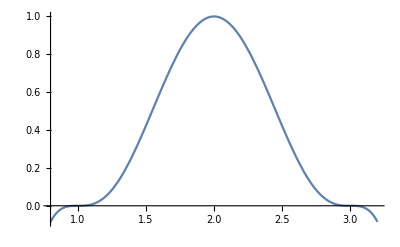

```mathematica
Plot[
Evaluate[(eq13[[2]] /. v1-> 1 /. v2-> 3) ] , {v,0.8,3.2}]
```